```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adityak/Aditya/git/root_tracking/Mathematica/SRSPM/Singularity_event

## Required libraries and functions:

```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
```

```mathematica
(*Run the following commands if MaTeX is not already installed and configured with Mathematica in your PC*)
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"/usr/bin/pdflatex"
]*)
```

```mathematica
<<MaTeX`
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

## Architecture of the SRSPM:

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.7, la->1.2};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
b = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

```mathematica
(b)[[2]]
```

{rb Cos[2 γb],rb Sin[2 γb],0}

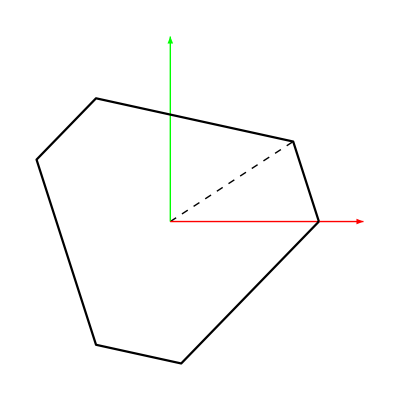

```mathematica
Show[Graphics[{Dashed, Line[{{0,0}, (b/.datap)[[2]][[1;;2]]}]}], Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black], AspectRatio->1, ImageResolution->600]
```

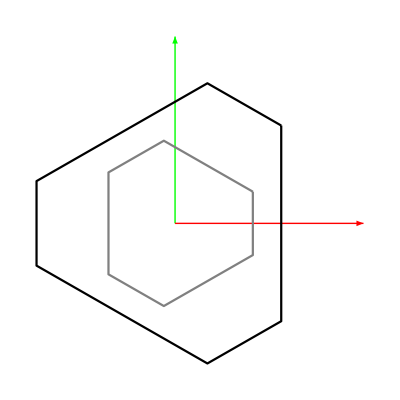

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
(*Locations of all the known ground joints*)
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;

tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];

b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];

al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
Show[Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Gray], AspectRatio->1, ImageResolution->600]
```

```mathematica
b/.datap
```

{{0.732576,0.680685,0},{0.223203,0.974772,0},{-0.955779,0.294087,0},{-0.955779,-0.294087,0},{0.223203,-0.974772,0},{0.732576,-0.680685,0}}

```mathematica
cords = {"x", "y", "z"};
```

```mathematica
acords = Table[Table[Symbol["a"<>ToString[j]<>cords[[i]]],{i, 3}],{j, 6}]
```

{{a1x,a1y,a1z},{a2x,a2y,a2z},{a3x,a3y,a3z},{a4x,a4y,a4z},{a5x,a5y,a5z},{a6x,a6y,a6z}}

```mathematica
Inner[Rule, Flatten[acords], Flatten[b/.datap], List]
```

{a1x→0.732576,a1y→0.680685,a1z→0,a2x→0.223203,a2y→0.974772,a2z→0,a3x→-0.955779,a3y→0.294087,a3z→0,a4x→-0.955779,a4y→-0.294087,a4z→0,a5x→0.223203,a5y→-0.974772,a5z→0,a6x→0.732576,a6y→-0.680685,a6z→0}

## Inverse Kinematics:

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
l= Table[Symbol["l"<>ToString[i]],{i, 6}];
(*a = Table[Symbol["a"<>ToString[i]],{i, 6}];*)
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
```

```mathematica
(*Considering ϕi, ψi and li's as the configuration space q*)
(*Rotation matrix of any leg li*)
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
(*Angular velocity Jacobian of each leg*)
Jωl = Table[SkewMat2vec[Simplify[T[Rl[[i]]].D[Rl[[i]],{Join[ϕ,ψ, l]}]]],{i, 6}];
(*a in global frame via b*)
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*The mid point of the top platform will be*)
ptp = Total[a]/6;
```

```mathematica
(*(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a65 = Simplify[((a[[6]]-a[[5]])/Sqrt[((b[[6]]-b[[5]]).(b[[6]]-b[[5]]))/.rb->rt/.γb->γt])];
a15 = Simplify[((a[[1]]-a[[5]])/Sqrt[((b[[1]]-b[[5]]).(b[[1]]-b[[5]]))/.rb->rt/.γb->γt])];
(*a12 and a13 are unit vectors, but the cross need not be a unit vector and hence the Rotation matrix columns need to be re-normalised*)
(*We need to find the magnitude of the second and the third axes*)*)
```

```mathematica
(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a56 = Simplify[((a[[5]]-a[[6]])/Sqrt[((b[[5]]-b[[6]]).(b[[5]]-b[[6]]))/.rb->rt/.γb->γt])];
a16 = Simplify[((a[[1]]-a[[6]])/Sqrt[((b[[1]]-b[[6]]).(b[[1]]-b[[6]]))/.rb->rt/.γb->γt])];
```

```mathematica
(*sinangle = Simplify[(Cross[(b[[6]]-b[[5]])/Sqrt[(b[[6]]-b[[5]]).(b[[6]]-b[[5]])], (b[[1]]-b[[5]])/Sqrt[(b[[1]]-b[[5]]).(b[[1]]-b[[5]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a65, a15]/sinangle];
Rtp = {a65,  Cross[zaxis, a65], zaxis};*)
```

```mathematica
sinangle = Simplify[(Cross[(b[[1]]-b[[6]])/Sqrt[(b[[1]]-b[[6]]).(b[[1]]-b[[6]])], (b[[5]]-b[[6]])/Sqrt[(b[[5]]-b[[6]]).(b[[5]]-b[[6]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a16, a56]/sinangle];
Rtp = { Cross[a16, zaxis],a16, zaxis};
```

```mathematica
(*Now that we have obtained the rotation matrix, we can find the angular velocity Jacobian of the top plate*)
Jωt = SkewMat2vec[T[Rtp].D[Rtp,{Join[ϕ, ψ, l]}]];
```

```mathematica
(*CoM of the two parts of the prismatic joints*)
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
Jpai = D[pa, {Join[ϕ, ψ, l]}];
Jpbi = D[pb, {Join[ϕ, ψ, l]}];
Jtp = D[ptp,  {Join[ϕ, ψ, l]}];
```

```mathematica
(*To generate the test data for this system*)
tpdat = {c1->0, c2->0, c3->0, x->0, y->0, z->1.1};
```

```mathematica
qrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
q = Join[ϕ, ψ, l]/.qrule;
```

```mathematica
Amat = vec2SkewMat[{c1, c2, c3}];
Rdat = Simplify[Inverse[(IdentityMatrix[3]-Amat)].(IdentityMatrix[3]+Amat)];
Simplify[Rdat.T[Rdat]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Rtps = Rtp/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.tpdat;
aldat = al/.datap;
ag =Simplify[Table[{x, y, z}+Rdat.aldat[[i]],{i, 6}]]/.tpdat;
bdat = b/.datap;
```

```mathematica
(*Formulating the constraint equations*)
```

```mathematica
η1 = Join[Simplify[Expand[Table[(a[[i]]-a[[i+1]]).(a[[i]]-a[[i+1]])-(al[[i]]-al[[i+1]]).(al[[i]]-al[[i+1]]),{i, 5}]]], {Simplify[Expand[(a[[6]]-a[[1]]).(a[[6]]-a[[1]])-(al[[6]]-al[[1]]).(al[[6]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[3]]).(a[[1]]-a[[3]])-(al[[3]]-al[[1]]).(al[[3]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[4]]).(a[[1]]-a[[4]])-(al[[1]]-al[[4]]).(al[[1]]-al[[4]])]], Simplify[Expand[(a[[1]]-a[[5]]).(a[[1]]-a[[5]])-(al[[1]]-al[[5]]).(al[[1]]-al[[5]])]], Expand[(a[[1]]-a[[3]]).Cross[a[[1]]-a[[2]], a[[1]]-a[[4]]]], Expand[(a[[1]]-a[[4]]).Cross[a[[1]]-a[[3]], a[[1]]-a[[5]]]], Expand[(a[[1]]-a[[5]]).Cross[a[[1]]-a[[4]], a[[1]]-a[[6]]]]}];
```

```mathematica
ηconfig = η1/.datap/.leglparam/.legmparam/.tpmparam/.qrule;
```

```mathematica
(*Therefore the sample solution satisfies the constraint equations*)
```

```mathematica
(*ηconfig/.datap/.leglparam/.legmparam/.tpmparam/.sampledat/.qrule*)
```

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}]; (*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]][t]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]][t]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]][t]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]][t]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
(*iksolver module*)
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
atps = Table[pc+Rtp2.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp2 = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
pc = {x, y, z};
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp2.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating constraints in the extended configuration space*)
```

```mathematica
ηext = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
qx = {x, y, z, c1, c2, c3};
```

```mathematica
samplex = Inner[Rule, qx, {0,0,0.75,0,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]][[;;-2]])/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cψval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{l1, _Complex},{l2, _Complex},{l3, _Complex},{l4, _Complex},{l5, _Complex},{l6, _Complex}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cϕval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{ψ1, _Complex},{ψ2, _Complex},{ψ3, _Complex},{ψ4, _Complex},{ψ5, _Complex},{ψ6, _Complex}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksolC[x_] := Module[{lvals, ψvals, ϕvals, xrule, lrule, ψrule},
xrule = Inner[Rule, qx, x, List];
lvals = l/.lval/.xrule;
lrule = Inner[Rule, l, lvals, List];
ψvals = ψ/.ψval/.Join[xrule, lrule];
ψrule = Inner[Rule, ψ, ψvals, List];
ϕvals = ϕ/.ϕval/.Join[xrule,ψrule];
Return[Join[ϕvals, ψvals, lvals]]
]
```

```mathematica
(*verifying roots taken from Anirbans codes*)
```

```mathematica
roots = ({{x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
rootsC = ({{x->1.8700438348728161, y->-0.5235870043873335, z->0.-0.926898973258719 ⅈ, c1->0.-0.10569096861540776 ⅈ, c2->0.+0.7154784037290103 ⅈ, c3->0}, {x->1.8700438348728161, y->-0.5235870043873335, z->0.+0.926898973258719 ⅈ, c1->0.+0.10569096861540776 ⅈ, c2->0.-0.7154784037290103 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.-0.9685245785328371 ⅈ, c1->0.-0.6638886705593215 ⅈ, c2->0.-0.3422565386596551 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.+0.9685245785328371 ⅈ, c1->0.+0.6638886705593215 ⅈ, c2->0.+0.3422565386596551 ⅈ, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.-1.3894731322781502 ⅈ, c1->0.+0.6338547336758182 ⅈ, c2->0.-0.42758251604766423 ⅈ, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.+1.3894731322781502 ⅈ, c1->0.-0.6338547336758182 ⅈ, c2->0.+0.42758251604766423 ⅈ, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
ikroots = Table[Inner[Rule, Join[ϕ, ψ, l], iksolC[qx/.roots[[i]]], List], {i, Length[roots]}];
```

```mathematica
iksolC[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]
```

```mathematica
initpose=Join[qx/.roots[[2]],iksolC[qx/.roots[[2]]]];
initposes=Table[Join[qx/.roots[[ii]],iksolC[qx/.roots[[ii]]]],{ii,8}];
initposeC = Join[qx/.rootsC[[1]],iksolC[qx/.rootsC[[1]]]];
```

```mathematica
xbrule = Table[{Symbol["xb"<>ToString[i]], Symbol["yb"<>ToString[i]], Symbol["zb"<>ToString[i]]},{i, 1, 6}];
xtrule = Table[{Symbol["xt"<>ToString[i]], Symbol["yt"<>ToString[i]], Symbol["zt"<>ToString[i]]},{i, 1, 6}];
```

```mathematica
top = Table[Inner[Rule, xtrule[[i]], (a/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xt1→0.628916,yt1→-0.430149,zt1→0.91962},{xt2→0.449784,yt2→-0.557918,zt2→0.245515},{xt3→0.127107,yt3→-0.844307,zt3→0.153522},{xt4→-0.212447,yt4→-1.17689,zt4→0.679753},{xt5→-0.101009,yt5→-1.09741,zt5→1.09912},{xt6→0.417678,yt6→-0.637052,zt6→1.24699}}

```mathematica
base = Table[Inner[Rule, xbrule[[i]], (b/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xb1→0.732576,yb1→0.680685,zb1→0},{xb2→0.223203,yb2→0.974772,zb2→0},{xb3→-0.955779,yb3→0.294087,zb3→0},{xb4→-0.955779,yb4→-0.294087,zb4→0},{xb5→0.223203,yb5→-0.974772,zb5→0},{xb6→0.732576,yb6→-0.680685,zb6→0}}

```mathematica
roots[[1]]
```

{x→0.218338,y→-0.790621,z→0.724086,c1→-0.715499,c2→-0.645258,c3→0}

```mathematica
Rationalize[base, 0.01]
```

{{xb1→8/11,yb1→11/16,zb1→0},{xb2→2/9,yb2→28/29,zb2→0},{xb3→-19/20,yb3→2/7,zb3→0},{xb4→-19/20,yb4→-2/7,zb4→0},{xb5→2/9,yb5→-29/30,zb5→0},{xb6→8/11,yb6→-13/19,zb6→0}}

```mathematica
Max[Table[ηconfig/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.ikroots[[i]], {i, Length[ikroots]}]];
```

```mathematica
roots//Dimensions
```

{8,6}

```mathematica
(*All the roots satisfy our constraint equation*)
```

```mathematica
(*{x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]}*)
```

## Compiled functions

```mathematica
qrule = Inner[Rule, q, Join[ϕ, ψ, l], List];
qvar = q/.qrule;
qfull = Join[qx, qvar];
```

```mathematica
cηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηconfig/.qrule], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηconfig = D[ηconfig/.qrule,{ q[[;;-7]]/.qrule}];
```

```mathematica
cJηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηconfig], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
cηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηext = D[ηext,{ Join[qx, q[[;;-7]]/.qrule]}];
```

```mathematica
Jηext//Variables
```

{c1,c2,c3,l1,l2,l3,l4,l5,l6,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
cJηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

## Plotting the SRSPM:

```mathematica
(*Plotting SRSPM from discretisation starting position*)
```

```mathematica
plotsrspm[qvals_,range_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-range, range}, {-range,range}, {-range,range}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis]
]
```

```mathematica
(*Plotting the constraints*)
```

```mathematica
plotconstraints[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis, constraints, oval, pts},
oval=5;
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3/oval],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, 2,6}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85/oval],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, 2,6}];
(*Joints*)
jointsbase = Table[Graphics3D[{Opacity[1/oval],Sphere[bval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];
jointstop = Table[Graphics3D[{Opacity[1/oval],Sphere[aval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting constraints*)
constraints = Show[Graphics3D[{Gray,Arrowheads[0.04],Arrow[Tube[{{0,0,0},bval[[1]]},0.025]]}], Graphics3D[{Purple,Arrowheads[0.045],Arrow[Tube[{bval[[1]], (aval/.qvals)[[1]]},0.025]]}], Graphics3D[{Black,Arrowheads[0.045],Arrow[Tube[{(aval/.qvals)[[1]], {x,y,z}/.qvals},0.025]]}], Graphics3D[{Brown,Arrowheads[0.045],Arrow[Tube[{{0,0,0}, {x,y,z}/.qvals},0.025]]}]];
(*Mid points*)
pts = Show[Graphics3D[{Red, Opacity[0.5],Sphere[{0,0,0}, 0.06]}], Graphics3D[{Red, Opacity[0.5],Sphere[Mean[aval/.qvals], 0.06]}]];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis, constraints, pts]
]
```

```mathematica
pt = {0.2,0.2,1.1,0.1,0,0}
cpose = Inner[Rule, qfull,  Join[pt, iksolC[pt]], List];
plotconstraints[Chop[cpose]]
```

{0.2,0.2,1.1,0.1,0,0}

-Graphics3D-

```mathematica
plotsrspm[Chop[Inner[Rule, qfull, initpose, List]],1.6]
```

-Graphics3D-

## Path generation

```mathematica
(*Select a circle, do the IK and get the values and fit a function to those leg values. Now track these functions with other initial conditions*)
```

```mathematica
scale = 0.2;
```

```mathematica
(* Circular path with changing orientation *)
parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*Cos[α], scale*Sin[α],scale*Sin[2*α]};
```

```mathematica
(* Circular path with constant orientation *)
(* parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*1, scale*0,scale*0}; *)
```

```mathematica
(* Straight line path moving towards singularity *)
(* parampath = {scale-α,α, 1.28-α, scale*1, scale*0,scale*0}; *)
```

```mathematica
pathpts = Table[parampath/.α->ii, {ii, 0, 2π, 2π/50}];
```

```mathematica
iksolC[pathpts[[1]]][[-6;;]]
```

{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
pathplt=Graphics3D[{Red, Sphere[Chop[pathpts[[;;]]][[;;, ;;3]], 0.025]}]
```

-Graphics3D-

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[pathpts[[u]], iksolC[pathpts[[u]]]], List],1.6],Graphics3D[{Red, Sphere[Chop[pathpts[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
(*Selected pose for plotting*)
```

```mathematica
(*plotsrspm[Inner[Rule, qfull, Join[pathpts[[43]], iksol[pathpts[[43]]]], List],1.6]*)
```

```mathematica
(*get all the leg array for the circular motion*)
```

```mathematica
(*legvals = Table[Join[{i-1}, {iksol[pathpts[[i]]][[-6;;]]}], {i, Length[pathpts]}];*)
legvals = Table[iksolC[pathpts[[i]]][[-6;;]], {i, Length[pathpts]}];
```

```mathematica
legvals[[1]]
```

{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
initpose=Join[pathpts[[1]], iksolC[pathpts[[1]]]]
```

{0.2,0.,1.28,0.2,0.,0.,0.00305624-8.22748×10^-17 ⅈ,-0.0668855-2.77949×10^-17 ⅈ,0.456963-1.1835×10^-16 ⅈ,0.546956-1.39651×10^-17 ⅈ,-0.0946901-1.93388×10^-16 ⅈ,0.00349011-1.87171×10^-16 ⅈ,0.336276+1.47256×10^-17 ⅈ,0.286891-5.66207×10^-17 ⅈ,-0.0210274-2.43773×10^-17 ⅈ,0.0247844-1.74336×10^-16 ⅈ,-0.395383-1.37395×10^-16 ⅈ,-0.379795-1.10578×10^-16 ⅈ,1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
(*legvals//MatrixForm*)
(*legvals//Im//Flatten//CForm*)
```

```mathematica
(*legfunc = Interpolation[legvals]*)
```

## Newton-Raphson method for root tracking

## Real roots:

```mathematica
(*Now root tracking all the 8 solutions with this leg interpolation for the 50 points*)
```

```mathematica
(*Newton-Raphson method*)
```

```mathematica
NRTracking[thetai_, phii_, eta_, Jeta_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
(*Takes in eta and Jeta as compiled functions*)
nvec = eta@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[(Norm[nvec]≥ 10^-10)&&(loopcounter≤100),
loopcounter++;
Jmat =  Jeta@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = eta@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
(*Tracking using the extended configuration space*)
```

```mathematica
Jηext//Dimensions
Jηext//Variables
```

{18,18}

{c1,c2,c3,l1,l2,l3,l4,l5,l6,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

### Root 1:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[1,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.54665×10^-15

```mathematica
(* Function to track a particular root given a table of the leg lengths for the entire path. *)
TrackPathRoot[initpose_,legvals_,steps_]:=
Module[{rtempϕ,rϕlist,ii},
rtempϕ = initpose;
rϕlist = {rtempϕ};
For[ii=2,ii≤steps, ii++, 
rtempϕ = NRTracking[legvals[[ii]], rtempϕ, cηext, cJηext];
AppendTo[rϕlist, rtempϕ];
];
Return[rϕlist];
]
```

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r1tempϕ = initposes[[1,;;-7]];
tic[]
r1ϕlist = TrackPathRoot[r1tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.02681 seconds.

CPU time consumed: 0.026822 seconds.

```mathematica
r1xlist = r1ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r1trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r1xlist[[u]], iksolC[r1xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[Chop[r1xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r1xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 2:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[2,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

9.22299×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r2tempϕ = initposes[[2,;;-7]];
tic[]
r2ϕlist = TrackPathRoot[r2tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.02018 seconds.

CPU time consumed: 0.020174 seconds.

```mathematica
r2xlist = r2ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r2trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r2xlist[[u]], iksolC[r2xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[Chop[r2xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r2xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 3:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[3,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.11426×10^-15

```mathematica
Length[legvals]
```

51

```mathematica
initposes[[3,;;-7]]
```

{-0.513695,-0.519996,-0.798723,-0.333759,-0.951699,0,-1.88547-1.05103×10^-16 ⅈ,-2.65366+2.74726×10^-17 ⅈ,2.78228+1.86009×10^-17 ⅈ,2.89251-1.51877×10^-16 ⅈ,-2.20522+5.34046×10^-17 ⅈ,-1.74294-1.42102×10^-16 ⅈ,0.61606-1.17742×10^-16 ⅈ,0.697469-2.13889×10^-16 ⅈ,0.419763+1.94314×10^-17 ⅈ,0.5377-1.52741×10^-16 ⅈ,0.0705025-6.62747×10^-17 ⅈ,-0.103948+3.0597×10^-18 ⅈ}

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r3tempϕ = initposes[[3,;;-7]];
tic[]
r3ϕlist = TrackPathRoot[r3tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.02641 seconds.

CPU time consumed: 0.026408 seconds.

```mathematica
r3xlist = r3ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r3trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r3xlist[[u]], iksolC[r3xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[Chop[r3xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r3xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 4:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[4,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.20587×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r4tempϕ = initposes[[4,;;-7]];
tic[]
r4ϕlist = TrackPathRoot[r4tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.02679 seconds.

CPU time consumed: 0.026812 seconds.

```mathematica
r4xlist = r4ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r4trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r4xlist[[u]], iksolC[r4xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[Chop[r4xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r4xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 5:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[5,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

9.66454×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r5tempϕ = initposes[[5,;;-7]];
tic[]
r5ϕlist = TrackPathRoot[r5tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.02028 seconds.

CPU time consumed: 0.0203 seconds.

```mathematica
r5xlist = r5ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r5trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r5xlist[[u]], iksolC[r5xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[Chop[r5xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r5xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 6:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[6,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.097×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r6tempϕ = initposes[[6,;;-7]];
tic[]
r6ϕlist = TrackPathRoot[r6tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.02895 seconds.

CPU time consumed: 0.028949 seconds.

```mathematica
r6xlist = r6ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r6trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r6xlist[[u]], iksolC[r6xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[Chop[r6xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r6xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 7:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[7,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.47006×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r7tempϕ = initposes[[7,;;-7]];
tic[]
r7ϕlist = TrackPathRoot[r7tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.02754 seconds.

CPU time consumed: 0.027532 seconds.

```mathematica
r7xlist = r7ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r7trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r7xlist[[u]], iksolC[r7xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[Chop[r7xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r7xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 8:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[8,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.28805×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r8tempϕ = initposes[[8,;;-7]];
tic[]
r8ϕlist = TrackPathRoot[r8tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.02492 seconds.

CPU time consumed: 0.024929 seconds.

```mathematica
r8xlist = r8ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r8trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r8xlist[[u]], iksolC[r8xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[Chop[r8xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r8xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List],1.6],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

## Singularity manifold

```mathematica
g11 = Import["singmanifold_ddp_cords_0_2_0_0_0_0.m"]
```

-8.76498×10^-15+y^2 (1.7087×10^-14-0.0317581 z)+x^2 (9.22743×10^-15-1.73472×10^-18 z)+0.0364021 z-3.56473×10^-14 z^2-0.381097 z^3+x (-4.84335×10^-15+y (-0.0100837+5.59691×10^-14 z)+0.0671749 z-2.09902×10^-13 z^2)+y (0.00732243-1.11494×10^-13 z+0.23501 z^2)

```mathematica
lim=4;
cp=ContourPlot3D[g11==0,{x,-lim,lim},{y,-lim,lim},{z,-lim,lim},ContourStyle->{Green,Opacity[0.6]},PlotPoints->60];
```

```mathematica
xpose = {0.2,0,1.28,0.2,0,0};
Show[plotsrspm[Inner[Rule, qfull, Join[xpose, iksolC[xpose]], List]], cp,pathplt]
```

-Graphics3D-

### Checking if Det[Jηext] is 0 for random points on g11

```mathematica
randomnumbers=500;
xrandom=RandomReal[{-1.6,1.6},randomnumbers];
yrandom=RandomReal[{-1.6,1.6},randomnumbers];
zrandom=Table[z/.Solve[(g11/.Inner[Rule,{x,y},{xrandom[[ii]],yrandom[[ii]]},List])==0],{ii,randomnumbers}];
ptsrandom=Flatten[Table[Table[{xrandom[[ii]],yrandom[[ii]],zrandom[[ii]][[jj]]},{jj,3}],{ii,randomnumbers}],1];
randrule=Table[Inner[Rule,{x,y,z},ptsrandom[[ii]],List],{ii,randomnumbers}];
```

```mathematica
(* Checking if the obtained points lie on g11=0 *)
Table[g11/.randrule[[ii]],{ii,randomnumbers}]//Abs//Max
```

1.8735×10^-16

```mathematica
(* Checking if the random configurations satisfy the constraints *)
Table[Norm[cηext@@Join[({x,y,z,0.2,0,0}/.randrule[[ii]]),iksolC[({x,y,z,0.2,0,0}/.randrule[[ii]])]]],{ii,randomnumbers}]//Max
```

2.49398×10^-15

```mathematica
(* Now evaluating Det[Jηext] for these random points *)
randomDet=Table[Det[cJηext@@Join[({x,y,z,0.2,0,0}/.randrule[[ii]]),iksolC[({x,y,z,0.2,0,0}/.randrule[[ii]])]]],{ii,randomnumbers}];
randomDet//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.22597×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.07349×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Singularity Event Identification

```mathematica
(* Specify one branch of interest on which we are moving and try to warn if the branch will encounter a singularity. Also, try to locate the singularity (estimate it with reasonable accuracy) *)
```

```mathematica
(* finddistroots[allroots,intrestroot,qxORqfull]: Function to find the distance between the branch of interest and other branches *)
(* Description of the inputs:
	allroots - qfull for all the branches, at a particular instant
  intrestroot - The branch in which the manipulator is physically moving
	qxORqfull - A binary variable to decide which among qx or qfull is to be used for calculating the distance betweent the roots
*)
finddistroots[allroots_,intrestroot_,qxORqfull_]:=
Module[{n,ii,dist},
n=Length[allroots];
dist={};
For[ii=1,ii≤n,ii++,
If[ii≠intrestroot,
If[qxORqfull==1,
(* True *)AppendTo[dist,Norm[allroots[[intrestroot]]-allroots[[ii]]]];,
(* False *)AppendTo[dist,Norm[(allroots[[intrestroot]]-allroots[[ii]])[[1;;6]]]];
];
];
];
Return[dist]
];
```

```mathematica
(* Function to find the coefficients to the fitting quadratic function, which will be used to estimate the singularity *)
(* Description of the inputs:
	xlist - A list of 3 values of the path parameter (input variable)
  ylist - A list of the corresponding 3 values of the distance (output variable) 
*)
(* Description of the output:
{a1,a2,a3} - The coefficients of the quadratic equation which is satisfied by the 3 input points. 
          Equation of the form a1*α^2+a2*α+a3=d where α is the input variable and d is the output variable. 
*)
findextrapfuncCoeff[xlist_,ylist_]:=
Module[{a1,a2,a3,eq,x,y,coeff},
eq=a1*x^2+a2*x+a3-y;
coeff=Solve[{(eq/.Inner[Rule,{x,y},{xlist[[1]],ylist[[1]]},List]),(eq/.Inner[Rule,{x,y},{xlist[[2]],ylist[[2]]},List]),(eq/.Inner[Rule,{x,y},{xlist[[3]],ylist[[3]]},List])}=={0,0,0},{a1,a2,a3}];
Return[Flatten[{a1,a2,a3}/.coeff]];
];
```

```mathematica
NRallbranches[allbranches_,legvals_]:=
Module[{},
Return[Table[Join[NRTracking[legvals, allbranches[[ii]][[1;;18]], cηext, cJηext],legvals],{ii,Length[allbranches]}]]
];
```

```mathematica
Clear[intrestbranch,distroots,cnt,alphaI,alphaIminus1,alphaIminus2,alphaIplus1,distI,distIminus1,distIminus2,deldist,delalpha,predstep,grad,singbranch,dvals,alphavals,extrapcoeff,extrapfunc,solSing,estiqxSing,estialphaSing,estiqfullSing,singFlag]
```

```mathematica
(* Function to identify if a singularity is being encountered along the desired path. *)
(* Description of the inputs:
	allbranches - A table of qfull for all the branches, along the entire path
    intrestbranch - The branch in which the manipulator is physically moving
	pathparam - (α,initval,finalval,initstepsize)
	parampath - Path definition: The task space variables defined in terms of the path parameter
 qxORqfull - A binary variable to decide which among qx or qfull is to be used for calculating the distance betweent the roots
*)
singularityEventIdentifier[allbranches_,intrestbranch_,pathparam_,parampath_,qxORqfull_]:=
Module[{α,initval,finalval,stepsize,distroots,prevstep,cnt,alphaI,alphaIminus1,alphaIminus2,alphaIplus1,distI,distIminus1,distIminus2,deldist,delalpha,legvals,nextstep,predstep,grad,ii,singbranch,dvals,alphavals,extrapcoeff,extrapfunc,a1,a2,a3,solSing,estiqxSing,estialphaSing,estiqfullSing,singFlag,returnval,checkalpha,trackedbranch},
(* Defining a vector to store the distance between the branch of intrest and other branches *)
distroots={};
singbranch={};
returnval={};
trackedbranch={allbranches};
prevstep=allbranches;
{α,initval,finalval,stepsize}=pathparam;
(* At cnt=1, *)
alphaIminus1=initval;
alphaIminus2=initval;
(* Using only the task space variable to find the distance between the roots *)
distIminus1=finddistroots[prevstep,intrestbranch,qxORqfull];
distIminus2=distIminus1;
singFlag=0;
If[stepsize>0,checkalpha=alphaIminus1<finalval;,checkalpha=alphaIminus1>finalval;];
While[singFlag==0&&checkalpha,
alphaI=alphaIminus1+stepsize;
If[checkalpha,alphaIplus1=alphaI+stepsize,alphaIplus1=finalval];
delalpha=alphaI-alphaIminus1;
legvals=iksolC[parampath/.{α->alphaI}][[-6;;]];
nextstep=NRallbranches[prevstep,legvals];
trackedbranch=Append[trackedbranch,nextstep];
distI=finddistroots[nextstep,intrestbranch,0];
deldist=distI-distIminus1;
grad=Table[deldist[[ii]]/delalpha,{ii,1,Length[distI]}];
predstep=Table[distI[[ii]]+(alphaIplus1-alphaI)*grad[[ii]],{ii,1,Length[grad]}];
For[ii=0,ii≤Length[predstep],ii++,
If[predstep[[ii]]<0,
singFlag=1;
dvals={distIminus2[[ii]],distIminus1[[ii]],distI[[ii]]};
alphavals={alphaIminus2,alphaIminus1,alphaI};
extrapcoeff=findextrapfuncCoeff[alphavals,dvals];
extrapfunc=a1*α^2+a2*α+a3/.Inner[Rule,{a1,a2,a3},extrapcoeff,List];
solSing=Solve[extrapfunc==0,α];
estialphaSing=If[Abs[(α/.solSing[[1]])-alphaI]<Abs[(α/.solSing[[2]])-alphaI],solSing[[1]],solSing[[2]]];
estiqxSing=parampath/.estialphaSing;
estiqfullSing=Join[estiqxSing,iksolC[estiqxSing]];
If[ii≥intrestbranch,
AppendTo[singbranch,ii+1];AppendTo[returnval,{singFlag,estialphaSing,ii+1,estiqfullSing,trackedbranch}];Print["Singularity encountered, branches ",intrestbranch," and ",ii+1," are observed to merge."];,
AppendTo[singbranch,ii];AppendTo[returnval,{singFlag,estialphaSing,ii,estiqfullSing,trackedbranch}];Print["Singularity encountered, branches ",intrestbranch," and ",singbranch," are observed to merge."];
];
];
];
If[singFlag==0,
alphaIminus2=alphaIminus1;
alphaIminus1=alphaI;
If[stepsize>0,checkalpha=alphaIminus1<finalval;,checkalpha=alphaIminus1>finalval;];
prevstep=nextstep;
If[alphaIminus1==finalval,
returnval={0,Null,Null};
Print["No singularity encountered"]
];
distIminus2=distIminus1;
distIminus1=distI;,
Break;
];
];
Return[returnval];
];
```

## Locating the singularity for different type of paths

## Straight Line Path

### Defining the path

```mathematica
(* Straight line path moving towards singularity *)
parampath = {scale-α,α, 1.28-α, scale*1, scale*0,scale*0}; 
pathparam={α,0,π/3,π/150};
legvals = Table[iksolC[(parampath/.{α->ii})][[-6;;]],{ii,0,π/3,π/150}];
desiredpath=Table[(parampath/.{α->ii}),{ii,0,π/3,π/150}];
desiredpathplt=Graphics3D[{Blue,Thick,Line[desiredpath[[;;44,1;;3]]]},Boxed->False];
```

### Actual point of singularity along the path:

```mathematica
(* The value of path parameter when the path hits the singularity manifold *)
alphaSing=Solve[Expand[g11/.Inner[Rule,{x,y,z},parampath[[1;;3]],List]]==0,α]
```

{{α→0.798115},{α→1.16642-0.248537 ⅈ},{α→1.16642+0.248537 ⅈ}}

```mathematica
(* Task space configuration at the singularity *)
qxSing=parampath/.alphaSing[[1]]
```

{-0.598115,0.798115,0.481885,0.2,0.,0.}

```mathematica
(* The Active and passive joint parameters at the singularity *)
qfullSing=Join[qxSing,iksolC[qxSing]]//Chop
```

{-0.598115,0.798115,0.481885,0.2,0,0,-0.950867,-0.906905,-0.163079,-0.286329,-1.28847,-1.10707,-0.317943,-0.30101,-0.924925,-1.13072,-0.925127,-0.962679,1.02693,1.19475,1.04099,0.845481,1.55504,1.55375}

```mathematica
(* Verifying that the obtained point is indeed singular *)
cJηext@@qfullSing//Det
```

-4.27926×10^-14+0. ⅈ

### Using extrapolation strategy to estimate the location of the singularity

```mathematica
singularityEventIdentifier[Chop[initposes],2,pathparam,parampath,0]//Length
```

Singularity encountered, branches 2 and 4 are observed to merge.

1

```mathematica
(* Verifying that the "singularityEventIdentification" function is working and the estimated configuration is actually singular *)
{Singflag,Singalpha,Singbranch,qfullestimateSing}=singularityEventIdentifier[Chop[initposes],2,pathparam,parampath,0][[1]];
(* Substituting x,y,z in the singularity manifold *)
g11/.Inner[Rule,{x,y,z},qfullestimateSing[[1;;3]],List]
(* Evaluating the determinant of the constraint jacobian matrix *)
cJηext@@qfullestimateSing//Det
cJηext@@qfullestimateSing//SingularValueList//MinMax
```

Singularity encountered, branches 2 and 4 are observed to merge.

Set::shape: Lists {Singflag,Singalpha,Singbranch,qfullestimateSing} and {1,«3»,{{{0.218338,-0.790621,0.724086,-0.715499,-0.645258,0,-0.112247,0.745313,1.42996,0.830045,-0.28684,-0.247355,0.876191,1.35618,0.805412,0.719639,0.106613,-0.0339125,1.44582,1.56868,1.57865,1.33939,1.15248,1.28688},{«1»},«5»,{0.524434,0.268509,-1.0308,-0.603749,0.188561,0,2.94959,3.05267,«9»,-0.62811,1.44582,1.56868,1.57865,1.33939,1.15248,1.28688}},«38»}} are not the same shape.

Part::take: Cannot take positions 1 through 3 in qfullestimateSing.

Inner::heads: Heads Part and List at positions 3 and 2 are expected to be the same.

ReplaceAll::reps: {Inner[Rule,{x,y,z},qfullestimateSing⟦1;;3⟧,List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-8.76498×10^-15+y^2 (1.7087×10^-14-0.0317581 z)+x^2 (9.22743×10^-15-1.73472×10^-18 z)+0.0364021 z-3.56473×10^-14 z^2-0.381097 z^3+x (-4.84335×10^-15+y (-0.0100837+5.59691×10^-14 z)+0.0671749 z-2.09902×10^-13 z^2)+y (0.00732243-1.11494×10^-13 z+0.23501 z^2)/.Inner[Rule,{x,y,z},qfullestimateSing⟦1;;3⟧,List]

Det[qfullestimateSing]

{SingularValueList[qfullestimateSing],SingularValueList[qfullestimateSing]}

### What happens if we try to simulate beyond the singularity

```mathematica
trackedpath=TrackPathRoot[initposes[[2,;;-7]],legvals,44];
trackedpathplt=Graphics3D[{Red,Dashing[{0.001,0.001}],Thick,Line[Chop[trackedpath[[39;;,1;;3]]]]},Boxed->False,PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}]; 
trackedpathpltzoomed=Graphics3D[{Red,Dashed,Thick,Line[Chop[trackedpath[[39;;,1;;3]]]]},Boxed->False,PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}]; (* The diverging part of the tracked path *)
singpoint=Graphics3D[{Red,Sphere[{qxSing[[1;;3]]},0.003]}];
switchingbranch=Show[trackedpathplt,desiredpathplt,singpoint,cp,PlotRange->{{-2,0.8},{-0.6,2.2},{-0.9,1.9}}]
zoomedview=Show[trackedpathpltzoomed,desiredpathplt,singpoint,cp,PlotRange->{{-0.8,-0.4},{0.6,1},{0.7,0.3}}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[zoomedview,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
(*Export["Singularity_straight_path_zoomed.pdf",Rasterize[zoomedview,RasterSize->{1080,720}]]*)
```

## Circular Path

```mathematica
circularpath=Join[{0.2,-1,0.28}+{0,1,1}.axisToRotMat[{1,2,2}/Norm[{1,2,2}],α],{0.2,0,0}];
```

```mathematica
circularpath/.{α->0}
```

{0.2,0,1.28,0.2,0,0}

### Defining the path

```mathematica
(* Circular path moving through singularity *)
parampath =Join[{-0.8,0.3,0.28}+{1,-0.3,1}.axisToRotMat[{2,3,2}/Norm[{2,3,2}],α],{0.2,0,0}];
pathparam={α,0,2π,π/75};
legvals = Table[iksolC[(parampath/.{α->ii})][[-6;;]],{ii,2π,0,-π/75}];
desiredpath=Table[(parampath/.{α->ii}),{ii,2π,0,-π/75}];
desiredpathplt=Graphics3D[{Blue,Thick,Line[desiredpath[[;;,1;;3]]]},Boxed->False,PlotRange->{{-2.1, 2.1}, {-2.1,2.1}, {-2.1, 2.1}}];
srspminitialpose=plotsrspm[Inner[Rule, qfull,Join[desiredpath[[1]],iksolC[desiredpath[[1]]]], List],1.6];
```

```mathematica
parampath/.{α->0}
```

{0.2,0.,1.28,0.2,0,0}

```mathematica
Show[desiredpathplt,srspminitialpose,cp]
```

-Graphics3D-

```mathematica
(*Export["circular_path_s2_manifold.SVG",Show[desiredpathplt,srspminitialpose,cp]]*)
```

```mathematica
cirPathAnim=Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[desiredpath[[u]], iksolC[desiredpath[[u]]]], List],2.4],cp,Graphics3D[{Red, Sphere[Chop[desiredpath[[;;u]]][[;;, ;;3]], 0.025]}],ViewPoint->{2/3,3/3,4/3},ViewAngle->35*Degree,ViewCenter->{-0.2,0,0}],
{u, 1, Length[desiredpath], 1}]
```

```mathematica
(*Export["cirPathAnim.gif", cirPathAnim, "AnimationDuration"->10];*)
```

### Actual points of singularity along the path:

```mathematica
(* The value of path parameter when the path hits the singularity manifold *)
alphaSing=Solve[Expand[g11/.Inner[Rule,{x,y,z},parampath[[1;;3]],List]]==0,α]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→-1.47623},{α→-1.28564},{α→-0.741417},{α→2.55011},{α→2.96816-0.333855 ⅈ},{α→2.96816+0.333855 ⅈ}}

```mathematica
(* Task space configuration at the singularity *)
qxSing1=parampath/.alphaSing[[3]]
qxSing2=parampath/.alphaSing[[4]]
qxSing3=parampath/.alphaSing[[5]]
qxSing4=parampath/.alphaSing[[6]]
```

{0.622896,0.222343,0.52359,0.2,0,0}

{-1.44951,1.55021,0.604189,0.2,0,0}

{-1.2554-0.255206 ⅈ,1.72834-0.0497109 ⅈ,0.142886+0.329772 ⅈ,0.2,0,0}

{-1.2554+0.255206 ⅈ,1.72834+0.0497109 ⅈ,0.142886-0.329772 ⅈ,0.2,0,0}

```mathematica
(* The Active and passive joint parameters at the singularity *)
qfullSing1=Join[qxSing1,iksolC[qxSing1]]//Chop
qfullSing2=Join[qxSing2,iksolC[qxSing2]]//Chop
qfullSing3=Join[qxSing3,iksolC[qxSing3]]//Chop
qfullSing4=Join[qxSing4,iksolC[qxSing4]]//Chop
```

{0.622896,0.222343,0.52359,0.2,0,0,0.612016,0.40845,1.03804,1.23773,0.817318,0.771899,0.330151,0.2665,-0.194184,-0.158368,-0.985065,-0.851734,0.785786,0.841248,1.32425,1.19938,0.799505,0.929565}

{-1.44951,1.55021,0.604189,0.2,0,0,-1.17421,-1.1301,-0.910252,-1.11451,-1.35535,-1.26504,-0.541597,-0.519396,-0.919479,-0.960146,-0.838871,-0.865685,2.08171,2.22889,1.99099,1.85166,2.68065,2.66211}

{-1.2554-0.255206 ⅈ,1.72834-0.0497109 ⅈ,0.142886+0.329772 ⅈ,0.2,0,0,-1.3752+0.188805 ⅈ,-1.30812+0.159235 ⅈ,-1.11268+0.231465 ⅈ,-1.4093+0.399086 ⅈ,-1.58669+0.217754 ⅈ,-1.48973+0.215536 ⅈ,-0.701406+0.124955 ⅈ,-0.670223+0.119879 ⅈ,-1.14235+0.184987 ⅈ,-1.17693+0.153853 ⅈ,-0.956749+0.0862606 ⅈ,-0.995319+0.0985189 ⅈ,1.89424+0.202327 ⅈ,2.01926+0.22449 ⅈ,1.89517+0.104595 ⅈ,1.81028+0.0616405 ⅈ,2.64184+0.0996577 ⅈ,2.60931+0.107259 ⅈ}

{-1.2554+0.255206 ⅈ,1.72834+0.0497109 ⅈ,0.142886-0.329772 ⅈ,0.2,0,0,-1.3752-0.188805 ⅈ,-1.30812-0.159235 ⅈ,-1.11268-0.231465 ⅈ,-1.4093-0.399086 ⅈ,-1.58669-0.217754 ⅈ,-1.48973-0.215536 ⅈ,-0.701406-0.124955 ⅈ,-0.670223-0.119879 ⅈ,-1.14235-0.184987 ⅈ,-1.17693-0.153853 ⅈ,-0.956749-0.0862606 ⅈ,-0.995319-0.0985189 ⅈ,1.89424-0.202327 ⅈ,2.01926-0.22449 ⅈ,1.89517-0.104595 ⅈ,1.81028-0.0616405 ⅈ,2.64184-0.0996577 ⅈ,2.60931-0.107259 ⅈ}

```mathematica
(* Verifying that the obtained point is indeed singular *)
cJηext@@qfullSing1//Det
cJηext@@qfullSing2//Det
cJηext@@qfullSing3//Det
cJηext@@qfullSing4//Det
```

-1.20991×10^-13+0. ⅈ

-2.47727×10^-12+0. ⅈ

2.31122×10^-12-2.13514×10^-14 ⅈ

2.3145×10^-12+2.47238×10^-14 ⅈ

### Using extrapolation strategy to estimate the location of the singularity

```mathematica
singularityEventIdentifier[Chop[initposes],2,{α,0,-2π,-π/75},parampath,0][[1]]
```

Singularity encountered, branches 2 and 4 are observed to merge.

{1,4}
 |  |  |  |

```mathematica
Chop[initposes]//MatrixForm
```

(0.218338 | -0.790621 | 0.724086 | -0.715499 | -0.645258 | 0 | -0.112247 | 0.745313 | 1.42996 | 0.830045 | -0.28684 | -0.247355 | 0.876191 | 1.35618 | 0.805412 | 0.719639 | 0.106613 | -0.0339125 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
0.2 | 0 | 1.28 | 0.2 | 0 | 0 | 0.00305624 | -0.0668855 | 0.456963 | 0.546956 | -0.0946901 | 0.00349011 | 0.336276 | 0.286891 | -0.0210274 | 0.0247844 | -0.395383 | -0.379795 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
-0.513695 | -0.519996 | -0.798723 | -0.333759 | -0.951699 | 0 | -1.88547 | -2.65366 | 2.78228 | 2.89251 | -2.20522 | -1.74294 | 0.61606 | 0.697469 | 0.419763 | 0.5377 | 0.0705025 | -0.103948 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
0.524434 | 0.268509 | 1.0308 | 0.603749 | -0.188561 | 0 | 0.192004 | 0.0889258 | 0.682842 | 1.07125 | 0.558764 | 0.329797 | 0.275819 | 0.269746 | -0.139217 | -0.356444 | -1.01698 | -0.62811 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
0.2 | 0 | -1.28 | -0.2 | 0 | 0 | 3.13854 | -3.07471 | 2.68463 | 2.59464 | -3.0469 | 3.1381 | 0.336276 | 0.286891 | -0.0210274 | 0.0247844 | -0.395383 | -0.379795 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
-0.513695 | -0.519996 | 0.798723 | 0.333759 | 0.951699 | 0 | -1.25612 | -0.487928 | 0.359309 | 0.249078 | -0.93637 | -1.39865 | 0.61606 | 0.697469 | 0.419763 | 0.5377 | 0.0705025 | -0.103948 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
0.218338 | -0.790621 | -0.724086 | 0.715499 | 0.645258 | 0 | -3.02935 | 2.39628 | 1.71163 | 2.31155 | -2.85475 | -2.89424 | 0.876191 | 1.35618 | 0.805412 | 0.719639 | 0.106613 | -0.0339125 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
0.524434 | 0.268509 | -1.0308 | -0.603749 | 0.188561 | 0 | 2.94959 | 3.05267 | 2.45875 | 2.07034 | 2.58283 | 2.8118 | 0.275819 | 0.269746 | -0.139217 | -0.356444 | -1.01698 | -0.62811 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688)

```mathematica
parampath/.{α->0}
```

{0.2,0.,1.28,0.2,0,0}

#### Travelling in the negative direction (with respect to the path parameter α)

```mathematica
(* Verifying that the "singularityEventIdentification" function is working and the estimated configuration is actually singular *)
{Singflagneg,Singalphaneg,Singbranchneg,qfullestimateSingneg,trackedbranchesneg}=singularityEventIdentifier[Chop[initposes],2,{α,0,-2π,-π/175},parampath,0][[1]];
(* Substituting x,y,z in the singularity manifold *)
g11/.Inner[Rule,{x,y,z},qfullestimateSingneg[[1;;3]],List]
(* Evaluating the determinant of the constraint jacobian matrix *)
cJηext@@qfullestimateSingneg//Det
cJηext@@qfullestimateSingneg//SingularValueList//MinMax
```

Singularity encountered, branches 2 and 4 are observed to merge.

-3.1445×10^-7

6.21807×10^-7+6.1591×10^-18 ⅈ

{3.7563×10^-7,2.9047}

```mathematica
Floor[(α/.Singalphaneg)/(-π/175)]
```

41

```mathematica
qfullestimateSingneg
```

{0.622896,0.222342,0.523591,0.2,0,0,0.612015+4.51148×10^-17 ⅈ,0.408449-1.5034×10^-16 ⅈ,1.03804-1.00933×10^-16 ⅈ,1.23773-1.00144×10^-16 ⅈ,0.817315+1.89272×10^-17 ⅈ,0.771897+9.55239×10^-17 ⅈ,0.330152+5.62733×10^-17 ⅈ,0.266501+1.05951×10^-17 ⅈ,-0.194184-1.42568×10^-16 ⅈ,-0.158367-1.18696×10^-16 ⅈ,-0.985063-3.21939×10^-17 ⅈ,-0.851733+9.78206×10^-18 ⅈ,0.785787+0. ⅈ,0.841249+0. ⅈ,1.32425+0. ⅈ,1.19938+0. ⅈ,0.799505+0. ⅈ,0.929565+0. ⅈ}

```mathematica
trackedbranchesneg[[;;,2]]
```

{{0.2,0,1.28,0.2,0,0,0.00305624,-0.0668855,0.456963,0.546956,-0.0946901,0.00349011,0.336276,0.286891,-0.0210274,0.0247844,-0.395383,-0.379795,1.44582,1.56868,1.57865,1.33939,1.15248,1.28688},{0.215571+0. ⅈ,0.000136488+0. ⅈ,1.26422+0. ⅈ,0.2+0. ⅈ,1.35553×10^-16+0. ⅈ,1.16776×10^-16+0. ⅈ,0.0146332+0. ⅈ,-0.0571519+0. ⅈ,0.470287+0. ⅈ,0.56308+0. ⅈ,-0.0813021+0. ⅈ,0.016738+0. ⅈ,0.339792+0. ⅈ,0.289852+0. ⅈ,-0.0212098+0. ⅈ,0.0247788+0. ⅈ,-0.401282+0. ⅈ,-0.384445+0. ⅈ,1.43102+0. ⅈ,1.55262+0. ⅈ,1.57151+0. ⅈ,1.33418+0. ⅈ,1.13679+0. ⅈ,1.27243+0. ⅈ},{0.230933+0. ⅈ,0.000545909+0. ⅈ,1.24825+0. ⅈ,0.2+0. ⅈ,2.02114×10^-16+0. ⅈ,7.39776×10^-16+0. ⅈ,0.0263267+0. ⅈ,-0.0473469+0. ⅈ,0.483672+0. ⅈ,0.579276+0. ⅈ,-0.0676887+0. ⅈ,0.030164+0. ⅈ,0.343205+0. ⅈ,0.292714+0. ⅈ,-0.0215683+0. ⅈ,0.0245665+0. ⅈ,-0.407567+0. ⅈ,-0.389401+0. ⅈ,1.41613+0. ⅈ,1.53645+0. ⅈ,1.56438+0. ⅈ,1.32904+0. ⅈ,1.12125+0. ⅈ,1.25813+0. ⅈ},{0.246079+0. ⅈ,0.00122813+0. ⅈ,1.23208+0. ⅈ,0.2+0. ⅈ,3.37811×10^-17+0. ⅈ,-2.73733×10^-16+0. ⅈ,0.0381393+0. ⅈ,-0.0374696+0. ⅈ,0.497115+0. ⅈ,0.595541+0. ⅈ,-0.0538409+0. ⅈ,0.0437731+0. ⅈ,0.34651+0. ⅈ,0.295472+0. ⅈ,-0.022105+0. ⅈ,0.0241454+0. ⅈ,-0.414248+0. ⅈ,-0.394669+0. ⅈ,1.40115+0. ⅈ,1.52018+0. ⅈ,1.55727+0. ⅈ,1.32396+0. ⅈ,1.10588+0. ⅈ,1.24398+0. ⅈ},{0.261006+0. ⅈ,0.00218293+0. ⅈ,1.21572+0. ⅈ,0.2+0. ⅈ,1.04317×10^-16+0. ⅈ,3.22246×10^-16+0. ⅈ,0.0500734+0. ⅈ,-0.0275187+0. ⅈ,0.510615+0. ⅈ,0.611873+0. ⅈ,-0.0397492+0. ⅈ,0.0575705+0. ⅈ,0.349706+0. ⅈ,0.298125+0. ⅈ,-0.0228223+0. ⅈ,0.0235131+0. ⅈ,-0.421338+0. ⅈ,-0.400256+0. ⅈ,1.38608+0. ⅈ,1.5038+0. ⅈ,1.55017+0. ⅈ,1.31894+0. ⅈ,1.09069+0. ⅈ,1.22998+0. ⅈ},{0.275709+0. ⅈ,0.00341001+0. ⅈ,1.19918+0. ⅈ,0.2+0. ⅈ,1.00934×10^-16+0. ⅈ,2.09393×10^-16+0. ⅈ,0.0621316+0. ⅈ,-0.0174932+0. ⅈ,0.524172+0. ⅈ,0.628269+0. ⅈ,-0.0254036+0. ⅈ,0.0715615+0. ⅈ,0.352787+0. ⅈ,0.300668+0. ⅈ,-0.0237224+0. ⅈ,0.0226675+0. ⅈ,-0.428848+0. ⅈ,-0.406171+0. ⅈ,1.37092+0. ⅈ,1.48732+0. ⅈ,1.5431+0. ⅈ,1.314+0. ⅈ,1.0757+0. ⅈ,1.21615+0. ⅈ},{0.290183+0. ⅈ,0.00490896+0. ⅈ,1.18245+0. ⅈ,0.2+0. ⅈ,-2.46215×10^-17+0. ⅈ,1.33297×10^-16+0. ⅈ,0.0743164+0. ⅈ,-0.00739187+0. ⅈ,0.537783+0. ⅈ,0.644726+0. ⅈ,-0.0107936+0. ⅈ,0.0857515+0. ⅈ,0.35575+0. ⅈ,0.303098+0. ⅈ,-0.0248075+0. ⅈ,0.0216067+0. ⅈ,-0.436789+0. ⅈ,-0.41242+0. ⅈ,1.35568+0. ⅈ,1.47073+0. ⅈ,1.53604+0. ⅈ,1.30912+0. ⅈ,1.06091+0. ⅈ,1.20249+0. ⅈ},{0.304423+0. ⅈ,0.00667931+0. ⅈ,1.16556+0. ⅈ,0.2+0. ⅈ,-3.03681×10^-17+0. ⅈ,4.28306×10^-16+0. ⅈ,0.0866304+0. ⅈ,0.00278634+0. ⅈ,0.551446+0. ⅈ,0.661241+0. ⅈ,0.00409163+0. ⅈ,0.100146+0. ⅈ,0.358591+0. ⅈ,0.305411+0. ⅈ,-0.0260797+0. ⅈ,0.0203287+0. ⅈ,-0.445172+0. ⅈ,-0.41901+0. ⅈ,1.34036+0. ⅈ,1.45405+0. ⅈ,1.52902+0. ⅈ,1.30431+0. ⅈ,1.04635+0. ⅈ,1.18903+0. ⅈ},{0.318424+0. ⅈ,0.00872048+0. ⅈ,1.1485+0. ⅈ,0.2+0. ⅈ,9.80462×10^-17+0. ⅈ,3.82936×10^-16+0. ⅈ,0.0990764+0. ⅈ,0.0130426+0. ⅈ,0.565161+0. ⅈ,0.677811+0. ⅈ,0.0192638+0. ⅈ,0.114751+0. ⅈ,0.361304+0. ⅈ,0.307603+0. ⅈ,-0.0275412+0. ⅈ,0.0188317+0. ⅈ,-0.454008+0. ⅈ,-0.425947+0. ⅈ,1.32495+0. ⅈ,1.43727+0. ⅈ,1.52202+0. ⅈ,1.29958+0. ⅈ,1.03201+0. ⅈ,1.17576+0. ⅈ},{0.332182+0. ⅈ,0.0110318+0. ⅈ,1.13127+0. ⅈ,0.2+0. ⅈ,1.43588×10^-16+0. ⅈ,-5.47549×10^-17+0. ⅈ,0.111657+0. ⅈ,0.0233781+0. ⅈ,0.578925+0. ⅈ,0.694432+0. ⅈ,0.0347349+0. ⅈ,0.129573+0. ⅈ,0.363887+0. ⅈ,0.30967+0. ⅈ,-0.0291941+0. ⅈ,0.0171142+0. ⅈ,-0.463308+0. ⅈ,-0.433237+0. ⅈ,1.30947+0. ⅈ,1.4204+0. ⅈ,1.51505+0. ⅈ,1.29493+0. ⅈ,1.01793+0. ⅈ,1.1627+0. ⅈ},{0.345694+0. ⅈ,0.0136126+0. ⅈ,1.11389+0. ⅈ,0.2+0. ⅈ,2.07193×10^-16+0. ⅈ,2.64424×10^-16+0. ⅈ,0.124375+0. ⅈ,0.033794+0. ⅈ,0.592738+0. ⅈ,0.711101+0. ⅈ,0.0505179+0. ⅈ,0.144617+0. ⅈ,0.366334+0. ⅈ,0.311607+0. ⅈ,-0.0310404+0. ⅈ,0.0151746+0. ⅈ,-0.473081+0. ⅈ,-0.440887+0. ⅈ,1.29391+0. ⅈ,1.40344+0. ⅈ,1.50812+0. ⅈ,1.29036+0. ⅈ,1.00411+0. ⅈ,1.14987+0. ⅈ},{0.358953+0. ⅈ,0.0164619+0. ⅈ,1.09635+0. ⅈ,0.2+0. ⅈ,1.0702×10^-16+0. ⅈ,2.8264×10^-16+0. ⅈ,0.137234+0. ⅈ,0.0442915+0. ⅈ,0.606596+0. ⅈ,0.727815+0. ⅈ,0.0666262+0. ⅈ,0.15989+0. ⅈ,0.368639+0. ⅈ,0.313411+0. ⅈ,-0.033082+0. ⅈ,0.0130114+0. ⅈ,-0.483336+0. ⅈ,-0.448902+0. ⅈ,1.27827+0. ⅈ,1.38638+0. ⅈ,1.50122+0. ⅈ,1.28587+0. ⅈ,0.99057+0. ⅈ,1.13726+0. ⅈ},{0.371957+0. ⅈ,0.019579+0. ⅈ,1.07867+0. ⅈ,0.2+0. ⅈ,1.05879×10^-16+0. ⅈ,-1.95934×10^-16+0. ⅈ,0.150236+0. ⅈ,0.0548718+0. ⅈ,0.620499+0. ⅈ,0.744571+0. ⅈ,0.083074+0. ⅈ,0.175398+0. ⅈ,0.370798+0. ⅈ,0.315076+0. ⅈ,-0.0353209+0. ⅈ,0.0106236+0. ⅈ,-0.494081+0. ⅈ,-0.457286+0. ⅈ,1.26257+0. ⅈ,1.36924+0. ⅈ,1.49437+0. ⅈ,1.28146+0. ⅈ,0.977325+0. ⅈ,1.12491+0. ⅈ},{0.3847+0. ⅈ,0.0229626+0. ⅈ,1.06086+0. ⅈ,0.2+0. ⅈ,2.00522×10^-19+0. ⅈ,1.19221×10^-16+0. ⅈ,0.163384+0. ⅈ,0.0655362+0. ⅈ,0.634444+0. ⅈ,0.761365+0. ⅈ,0.0998762+0. ⅈ,0.191149+0. ⅈ,0.372806+0. ⅈ,0.316598+0. ⅈ,-0.037759+0. ⅈ,0.00801002+0. ⅈ,-0.505324+0. ⅈ,-0.466044+0. ⅈ,1.2468+0. ⅈ,1.35201+0. ⅈ,1.48755+0. ⅈ,1.27715+0. ⅈ,0.964393+0. ⅈ,1.11281+0. ⅈ},{0.397179+0. ⅈ,0.0266119+0. ⅈ,1.0429+0. ⅈ,0.2+0. ⅈ,1.75237×10^-16+0. ⅈ,4.37257×10^-16+0. ⅈ,0.176682+0. ⅈ,0.0762859+0. ⅈ,0.648429+0. ⅈ,0.778193+0. ⅈ,0.117049+0. ⅈ,0.207148+0. ⅈ,0.374656+0. ⅈ,0.317971+0. ⅈ,-0.040398+0. ⅈ,0.00516972+0. ⅈ,-0.51707+0. ⅈ,-0.475181+0. ⅈ,1.23096+0. ⅈ,1.3347+0. ⅈ,1.48078+0. ⅈ,1.27292+0. ⅈ,0.95179+0. ⅈ,1.10098+0. ⅈ},{0.40939+0. ⅈ,0.0305256+0. ⅈ,1.02482+0. ⅈ,0.2+0. ⅈ,3.03648×10^-16+0. ⅈ,3.48824×10^-16+0. ⅈ,0.190133+0. ⅈ,0.0871221+0. ⅈ,0.662453+0. ⅈ,0.795052+0. ⅈ,0.134608+0. ⅈ,0.223404+0. ⅈ,0.376342+0. ⅈ,0.319189+0. ⅈ,-0.0432397+0. ⅈ,0.00210196+0. ⅈ,-0.529323+0. ⅈ,-0.484698+0. ⅈ,1.21505+0. ⅈ,1.3173+0. ⅈ,1.47406+0. ⅈ,1.26878+0. ⅈ,0.939533+0. ⅈ,1.08943+0. ⅈ},{0.421329+0. ⅈ,0.0347024+0. ⅈ,1.00662+0. ⅈ,0.2+0. ⅈ,9.05903×10^-17+0. ⅈ,2.70968×10^-16+0. ⅈ,0.203739+0. ⅈ,0.0980463+0. ⅈ,0.676514+0. ⅈ,0.811939+0. ⅈ,0.152571+0. ⅈ,0.239922+0. ⅈ,0.377858+0. ⅈ,0.320248+0. ⅈ,-0.0462858+0. ⅈ,-0.00119384+0. ⅈ,-0.542088+0. ⅈ,-0.494598+0. ⅈ,1.19909+0. ⅈ,1.29983+0. ⅈ,1.46739+0. ⅈ,1.26473+0. ⅈ,0.927641+0. ⅈ,1.07817+0. ⅈ},{0.432991+0. ⅈ,0.039141+0. ⅈ,0.988297+0. ⅈ,0.2+0. ⅈ,2.63944×10^-16+0. ⅈ,2.00547×10^-16+0. ⅈ,0.217505+0. ⅈ,0.10906+0. ⅈ,0.69061+0. ⅈ,0.828849+0. ⅈ,0.170956+0. ⅈ,0.256712+0. ⅈ,0.379198+0. ⅈ,0.32114+0. ⅈ,-0.0495377+0. ⅈ,-0.00471812+0. ⅈ,-0.555364+0. ⅈ,-0.504883+0. ⅈ,1.18307+0. ⅈ,1.28228+0. ⅈ,1.46077+0. ⅈ,1.26078+0. ⅈ,0.916131+0. ⅈ,1.06723+0. ⅈ},{0.444374+0. ⅈ,0.0438399+0. ⅈ,0.969866+0. ⅈ,0.2+0. ⅈ,2.21185×10^-16+0. ⅈ,1.72889×10^-16+0. ⅈ,0.231433+0. ⅈ,0.120164+0. ⅈ,0.704737+0. ⅈ,0.845779+0. ⅈ,0.189784+0. ⅈ,0.27378+0. ⅈ,0.380353+0. ⅈ,0.32186+0. ⅈ,-0.052997+0. ⅈ,-0.00847111+0. ⅈ,-0.56915+0. ⅈ,-0.515552+0. ⅈ,1.16699+0. ⅈ,1.26466+0. ⅈ,1.45421+0. ⅈ,1.25693+0. ⅈ,0.905022+0. ⅈ,1.05661+0. ⅈ},{0.455473+0. ⅈ,0.0487978+0. ⅈ,0.95133+0. ⅈ,0.2+0. ⅈ,3.63672×10^-16+0. ⅈ,7.38606×10^-17+0. ⅈ,0.245527+0. ⅈ,0.131359+0. ⅈ,0.718896+0. ⅈ,0.862726+0. ⅈ,0.209074+0. ⅈ,0.291135+0. ⅈ,0.381318+0. ⅈ,0.3224+0. ⅈ,-0.056665+0. ⅈ,-0.0124529+0. ⅈ,-0.583444+0. ⅈ,-0.526606+0. ⅈ,1.15086+0. ⅈ,1.24697+0. ⅈ,1.4477+0. ⅈ,1.25318+0. ⅈ,0.894332+0. ⅈ,1.04632+0. ⅈ},{0.466286+0. ⅈ,0.0540128+0. ⅈ,0.932695+0. ⅈ,0.2+0. ⅈ,2.78767×10^-16+0. ⅈ,4.97156×10^-17+0. ⅈ,0.259791+0. ⅈ,0.142649+0. ⅈ,0.733083+0. ⅈ,0.879685+0. ⅈ,0.228848+0. ⅈ,0.308784+0. ⅈ,0.382083+0. ⅈ,0.322754+0. ⅈ,-0.0605432+0. ⅈ,-0.0166634+0. ⅈ,-0.598239+0. ⅈ,-0.538041+0. ⅈ,1.13468+0. ⅈ,1.22921+0. ⅈ,1.44126+0. ⅈ,1.24952+0. ⅈ,0.884081+0. ⅈ,1.03638+0. ⅈ},{0.476807+0. ⅈ,0.0594834+0. ⅈ,0.913967+0. ⅈ,0.2+0. ⅈ,5.56483×10^-16+0. ⅈ,2.30616×10^-16+0. ⅈ,0.274228+0. ⅈ,0.154032+0. ⅈ,0.747295+0. ⅈ,0.896654+0. ⅈ,0.249128+0. ⅈ,0.326736+0. ⅈ,0.382641+0. ⅈ,0.322913+0. ⅈ,-0.0646327+0. ⅈ,-0.0211022+0. ⅈ,-0.613527+0. ⅈ,-0.549854+0. ⅈ,1.11846+0. ⅈ,1.21138+0. ⅈ,1.43489+0. ⅈ,1.24598+0. ⅈ,0.874286+0. ⅈ,1.0268+0. ⅈ},{0.487035+0. ⅈ,0.0652079+0. ⅈ,0.895153+0. ⅈ,0.2+0. ⅈ,1.14947×10^-15+0. ⅈ,2.41796×10^-16+0. ⅈ,0.288843+0. ⅈ,0.165513+0. ⅈ,0.761532+0. ⅈ,0.913628+0. ⅈ,0.269938+0. ⅈ,0.345+0. ⅈ,0.382983+0. ⅈ,0.322871+0. ⅈ,-0.0689345+0. ⅈ,-0.025769+0. ⅈ,-0.629297+0. ⅈ,-0.562042+0. ⅈ,1.10219+0. ⅈ,1.19349+0. ⅈ,1.42858+0. ⅈ,1.24254+0. ⅈ,0.864967+0. ⅈ,1.01759+0. ⅈ},{0.496966+0. ⅈ,0.0711843+0. ⅈ,0.876258+0. ⅈ,0.2+0. ⅈ,1.63017×10^-15+0. ⅈ,2.82676×10^-16+0. ⅈ,0.303639+0. ⅈ,0.177091+0. ⅈ,0.775791+0. ⅈ,0.930604+0. ⅈ,0.291303+0. ⅈ,0.363584+0. ⅈ,0.3831+0. ⅈ,0.322618+0. ⅈ,-0.0734498+0. ⅈ,-0.030663+0. ⅈ,-0.645533+0. ⅈ,-0.574598+0. ⅈ,1.08588+0. ⅈ,1.17554+0. ⅈ,1.42234+0. ⅈ,1.23921+0. ⅈ,0.856142+0. ⅈ,1.00878+0. ⅈ},{0.506596+0. ⅈ,0.0774107+0. ⅈ,0.857288+0. ⅈ,0.2+0. ⅈ,3.01358×10^-15+0. ⅈ,7.17975×10^-16+0. ⅈ,0.31862+0. ⅈ,0.188768+0. ⅈ,0.79007+0. ⅈ,0.947579+0. ⅈ,0.313249+0. ⅈ,0.382497+0. ⅈ,0.382982+0. ⅈ,0.322146+0. ⅈ,-0.0781795+0. ⅈ,-0.0357833+0. ⅈ,-0.662217+0. ⅈ,-0.587514+0. ⅈ,1.06954+0. ⅈ,1.15754+0. ⅈ,1.41618+0. ⅈ,1.23598+0. ⅈ,0.847829+0. ⅈ,1.00036+0. ⅈ},{0.515922+0. ⅈ,0.0838852+0. ⅈ,0.83825+0. ⅈ,0.2+0. ⅈ,5.35136×10^-15+0. ⅈ,5.93612×10^-16+0. ⅈ,0.33379+0. ⅈ,0.200546+0. ⅈ,0.804366+0. ⅈ,0.964548+0. ⅈ,0.335803+0. ⅈ,0.401749+0. ⅈ,0.382618+0. ⅈ,0.321445+0. ⅈ,-0.0831242+0. ⅈ,-0.0411291+0. ⅈ,-0.679327+0. ⅈ,-0.600781+0. ⅈ,1.05316+0. ⅈ,1.13948+0. ⅈ,1.41009+0. ⅈ,1.23288+0. ⅈ,0.840047+0. ⅈ,0.992362+0. ⅈ},{0.524942+0. ⅈ,0.0906056+0. ⅈ,0.819149+0. ⅈ,0.2+0. ⅈ,9.9751×10^-15+0. ⅈ,7.74999×10^-16+0. ⅈ,0.349154+0. ⅈ,0.212427+0. ⅈ,0.818678+0. ⅈ,0.981509+0. ⅈ,0.358995+0. ⅈ,0.421349+0. ⅈ,0.381998+0. ⅈ,0.320505+0. ⅈ,-0.0882847+0. ⅈ,-0.0466989+0. ⅈ,-0.696839+0. ⅈ,-0.614388+0. ⅈ,1.03676+0. ⅈ,1.12138+0. ⅈ,1.40408+0. ⅈ,1.22988+0. ⅈ,0.832813+0. ⅈ,0.984787+0. ⅈ},{0.533653+0. ⅈ,0.0975698+0. ⅈ,0.799992+0. ⅈ,0.2+0. ⅈ,1.87039×10^-14+0. ⅈ,1.14127×10^-15+0. ⅈ,0.364716+0. ⅈ,0.224412+0. ⅈ,0.833003+0. ⅈ,0.998458+0. ⅈ,0.382854+0. ⅈ,0.441306+0. ⅈ,0.381111+0. ⅈ,0.319316+0. ⅈ,-0.0936615+0. ⅈ,-0.0524914+0. ⅈ,-0.714722+0. ⅈ,-0.628324+0. ⅈ,1.02033+0. ⅈ,1.10323+0. ⅈ,1.39816+0. ⅈ,1.227+0. ⅈ,0.826144+0. ⅈ,0.977652+0. ⅈ},{0.542051+0. ⅈ,0.104776+0. ⅈ,0.780786+0. ⅈ,0.2+0. ⅈ,3.53396×10^-14+0. ⅈ,2.03787×10^-15+0. ⅈ,0.380481+0. ⅈ,0.236503+0. ⅈ,0.847339+0. ⅈ,1.01539+0. ⅈ,0.407411+0. ⅈ,0.46163+0. ⅈ,0.379944+0. ⅈ,0.317866+0. ⅈ,-0.099255+0. ⅈ,-0.0585049+0. ⅈ,-0.732945+0. ⅈ,-0.642572+0. ⅈ,1.00388+0. ⅈ,1.08503+0. ⅈ,1.39232+0. ⅈ,1.22424+0. ⅈ,0.820055+0. ⅈ,0.970968+0. ⅈ},{0.550134+0. ⅈ,0.11222+0. ⅈ,0.761535+0. ⅈ,0.2+0. ⅈ,6.781×10^-14+0. ⅈ,3.24502×10^-15+0. ⅈ,0.396453+0. ⅈ,0.248703+0. ⅈ,0.861684+0. ⅈ,1.03231+0. ⅈ,0.432699+0. ⅈ,0.482332+0. ⅈ,0.378483+0. ⅈ,0.316142+0. ⅈ,-0.105066+0. ⅈ,-0.0647378+0. ⅈ,-0.75147+0. ⅈ,-0.657119+0. ⅈ,0.98742+0. ⅈ,1.0668+0. ⅈ,1.38657+0. ⅈ,1.22159+0. ⅈ,0.814561+0. ⅈ,0.964747+0. ⅈ},{0.5579+0. ⅈ,0.119902+0. ⅈ,0.742247+0. ⅈ,0.2+0. ⅈ,1.32036×10^-13+0. ⅈ,4.73634×10^-15+0. ⅈ,0.412638+0. ⅈ,0.261012+0. ⅈ,0.876036+0. ⅈ,1.0492+0. ⅈ,0.458751+0. ⅈ,0.503421+0. ⅈ,0.376717+0. ⅈ,0.314133+0. ⅈ,-0.111093+0. ⅈ,-0.0711879+0. ⅈ,-0.770256+0. ⅈ,-0.671945+0. ⅈ,0.970946+0. ⅈ,1.04853+0. ⅈ,1.38091+0. ⅈ,1.21907+0. ⅈ,0.809677+0. ⅈ,0.958999+0. ⅈ},{0.565346+0. ⅈ,0.127818+0. ⅈ,0.722927+0. ⅈ,0.2+0. ⅈ,2.64676×10^-13+0. ⅈ,7.09057×10^-15+0. ⅈ,0.429039+0. ⅈ,0.273433+0. ⅈ,0.890392+0. ⅈ,1.06607+0. ⅈ,0.485602+0. ⅈ,0.524907+0. ⅈ,0.374629+0. ⅈ,0.311825+0. ⅈ,-0.117338+0. ⅈ,-0.0778531+0. ⅈ,-0.78926+0. ⅈ,-0.687031+0. ⅈ,0.954467+0. ⅈ,1.03024+0. ⅈ,1.37535+0. ⅈ,1.21667+0. ⅈ,0.805415+0. ⅈ,0.953736+0. ⅈ},{0.572469+0. ⅈ,0.135966+0. ⅈ,0.703582+0. ⅈ,0.2+0. ⅈ,5.48136×10^-13+0. ⅈ,1.08586×10^-14+0. ⅈ,0.445664+0. ⅈ,0.285968+0. ⅈ,0.904751+0. ⅈ,1.08291+0. ⅈ,0.513288+0. ⅈ,0.546802+0. ⅈ,0.372205+0. ⅈ,0.309202+0. ⅈ,-0.1238+0. ⅈ,-0.084731+0. ⅈ,-0.808434+0. ⅈ,-0.702357+0. ⅈ,0.937986+0. ⅈ,1.01192+0. ⅈ,1.36988+0. ⅈ,1.21439+0. ⅈ,0.801786+0. ⅈ,0.948966+0. ⅈ},{0.579268+0. ⅈ,0.144343+0. ⅈ,0.684218+0. ⅈ,0.2+0. ⅈ,1.18702×10^-12+0. ⅈ,1.675×10^-14+0. ⅈ,0.462516+0. ⅈ,0.298619+0. ⅈ,0.91911+0. ⅈ,1.09972+0. ⅈ,0.541845+0. ⅈ,0.569116+0. ⅈ,0.369427+0. ⅈ,0.30625+0. ⅈ,-0.130479+0. ⅈ,-0.0918192+0. ⅈ,-0.827728+0. ⅈ,-0.717899+0. ⅈ,0.921511+0. ⅈ,0.993574+0. ⅈ,1.36452+0. ⅈ,1.21224+0. ⅈ,0.798801+0. ⅈ,0.9447+0. ⅈ},{0.585739+0. ⅈ,0.152947+0. ⅈ,0.664841+0. ⅈ,0.2+0. ⅈ,2.73076×10^-12+0. ⅈ,2.47316×10^-14+0. ⅈ,0.479603+0. ⅈ,0.311389+0. ⅈ,0.933467+0. ⅈ,1.1165+0. ⅈ,0.57131+0. ⅈ,0.591859+0. ⅈ,0.36628+0. ⅈ,0.302951+0. ⅈ,-0.137374+0. ⅈ,-0.0991149+0. ⅈ,-0.847089+0. ⅈ,-0.733633+0. ⅈ,0.905045+0. ⅈ,0.975216+0. ⅈ,1.35926+0. ⅈ,1.21022+0. ⅈ,0.796467+0. ⅈ,0.940944+0. ⅈ},{0.591882+0. ⅈ,0.161774+0. ⅈ,0.645458+0. ⅈ,0.2+0. ⅈ,6.82803×10^-12+0. ⅈ,3.63344×10^-14+0. ⅈ,0.496929+0. ⅈ,0.324279+0. ⅈ,0.947821+0. ⅈ,1.13324+0. ⅈ,0.601721+0. ⅈ,0.615042+0. ⅈ,0.362743+0. ⅈ,0.299289+0. ⅈ,-0.144484+0. ⅈ,-0.106615+0. ⅈ,-0.866462+0. ⅈ,-0.749533+0. ⅈ,0.888597+0. ⅈ,0.956847+0. ⅈ,1.3541+0. ⅈ,1.20832+0. ⅈ,0.794791+0. ⅈ,0.937708+0. ⅈ},{0.597693+0. ⅈ,0.170822+0. ⅈ,0.626074+0. ⅈ,0.2+0. ⅈ,1.92157×10^-11+0. ⅈ,4.87829×10^-14+0. ⅈ,0.514501+0. ⅈ,0.337293+0. ⅈ,0.962169+0. ⅈ,1.14994+0. ⅈ,0.633113+0. ⅈ,0.638676+0. ⅈ,0.358798+0. ⅈ,0.295243+0. ⅈ,-0.15181+0. ⅈ,-0.114317+0. ⅈ,-0.885788+0. ⅈ,-0.765573+0. ⅈ,0.872171+0. ⅈ,0.938472+0. ⅈ,1.34905+0. ⅈ,1.20655+0. ⅈ,0.793778+0. ⅈ,0.934996+0. ⅈ},{0.603172+0. ⅈ,0.180088+0. ⅈ,0.606697+0. ⅈ,0.2+0. ⅈ,6.42976×10^-11+0. ⅈ,4.65377×10^-14+0. ⅈ,0.532325+0. ⅈ,0.350434+0. ⅈ,0.976509+0. ⅈ,1.1666+0. ⅈ,0.665525+0. ⅈ,0.662771+0. ⅈ,0.354423+0. ⅈ,0.290793+0. ⅈ,-0.15935+0. ⅈ,-0.122218+0. ⅈ,-0.905011+0. ⅈ,-0.781724+0. ⅈ,0.855774+0. ⅈ,0.920098+0. ⅈ,1.34412+0. ⅈ,1.20491+0. ⅈ,0.79343+0. ⅈ,0.932815+0. ⅈ},{0.608315+0. ⅈ,0.189569+0. ⅈ,0.587332+0. ⅈ,0.2+0. ⅈ,8.01335×10^-16+0. ⅈ,1.80388×10^-16+0. ⅈ,0.550409+0. ⅈ,0.363703+0. ⅈ,0.99084+0. ⅈ,1.18322+0. ⅈ,0.698991+0. ⅈ,0.687339+0. ⅈ,0.349596+0. ⅈ,0.285918+0. ⅈ,-0.167103+0. ⅈ,-0.130313+0. ⅈ,-0.92407+0. ⅈ,-0.797957+0. ⅈ,0.839414+0. ⅈ,0.901731+0. ⅈ,1.3393+0. ⅈ,1.20341+0. ⅈ,0.793749+0. ⅈ,0.931168+0. ⅈ},{0.613123+0. ⅈ,0.199261+0. ⅈ,0.567985+0. ⅈ,0.2+0. ⅈ,-2.90603×10^-16+0. ⅈ,-7.03731×10^-17+0. ⅈ,0.568759+0. ⅈ,0.377105+0. ⅈ,1.00516+0. ⅈ,1.19979+0. ⅈ,0.733545+0. ⅈ,0.71239+0. ⅈ,0.344294+0. ⅈ,0.280593+0. ⅈ,-0.175068+0. ⅈ,-0.1386+0. ⅈ,-0.942905+0. ⅈ,-0.814242+0. ⅈ,0.823099+0. ⅈ,0.883376+0. ⅈ,1.3346+0. ⅈ,1.20203+0. ⅈ,0.794733+0. ⅈ,0.93006+0. ⅈ},{0.617593+0. ⅈ,0.209163+0. ⅈ,0.548663+0. ⅈ,0.2+0. ⅈ,2.10109×10^-13+0. ⅈ,1.17701×10^-16+0. ⅈ,0.587382+0. ⅈ,0.390642+0. ⅈ,1.01946+0. ⅈ,1.21632+0. ⅈ,0.769219+0. ⅈ,0.737935+0. ⅈ,0.33849+0. ⅈ,0.274794+0. ⅈ,-0.183243+0. ⅈ,-0.147075+0. ⅈ,-0.961459+0. ⅈ,-0.83055+0. ⅈ,0.806836+0. ⅈ,0.865042+0. ⅈ,1.33002+0. ⅈ,1.20079+0. ⅈ,0.796381+0. ⅈ,0.929493+0. ⅈ},{0.621723+0. ⅈ,0.21927+0. ⅈ,0.529372+0. ⅈ,0.2+0. ⅈ,1.35024×10^-12+0. ⅈ,3.23825×10^-16+0. ⅈ,0.606287+0. ⅈ,0.404318+0. ⅈ,1.03376+0. ⅈ,1.23279+0. ⅈ,0.806041+0. ⅈ,0.763983+0. ⅈ,0.332159+0. ⅈ,0.268493+0. ⅈ,-0.191628+0. ⅈ,-0.155734+0. ⅈ,-0.979674+0. ⅈ,-0.846849+0. ⅈ,0.790634+0. ⅈ,0.846735+0. ⅈ,1.32556+0. ⅈ,1.19969+0. ⅈ,0.798686+0. ⅈ,0.929467+0. ⅈ}}

```mathematica
parampath[[1;;3]]
```

{0.2-9/17 (1-Cos[α])-(3 Sin[α])/(√17)-0.3 (6/17 (1-Cos[α])+(2 Sin[α])/(√17)),0.3-0.3 (1-8/17 (1-Cos[α]))+12/17 (1-Cos[α]),1.28-9/17 (1-Cos[α])+(3 Sin[α])/(√17)-0.3 (6/17 (1-Cos[α])-(2 Sin[α])/(√17))}

```mathematica
Graphics3D[{Green,Sphere[parampath[[1;;3]], 0.025]}]/.{α->0}
```

-Graphics3D-

{{0.2,0,1.28},{0.215571+0. ⅈ,0.000136488+0. ⅈ,1.26422+0. ⅈ},{0.230933+0. ⅈ,0.000545909+0. ⅈ,1.24825+0. ⅈ}}

```mathematica
trackedbranchesneg[[;;,2]][[1]]
```

{0.2,0,1.28,0.2,0,0,0.00305624,-0.0668855,0.456963,0.546956,-0.0946901,0.00349011,0.336276,0.286891,-0.0210274,0.0247844,-0.395383,-0.379795,1.44582,1.56868,1.57865,1.33939,1.15248,1.28688}

```mathematica
qfull
```

{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6}

```mathematica
Inner[Rule, qfull, Chop[trackedbranchesneg[[;;,2]][[1]]], List]
```

{x→0.2,y→0,z→1.28,c1→0.2,c2→0,c3→0,ϕ1→0.00305624,ϕ2→-0.0668855,ϕ3→0.456963,ϕ4→0.546956,ϕ5→-0.0946901,ϕ6→0.00349011,ψ1→0.336276,ψ2→0.286891,ψ3→-0.0210274,ψ4→0.0247844,ψ5→-0.395383,ψ6→-0.379795,l1→1.44582,l2→1.56868,l3→1.57865,l4→1.33939,l5→1.15248,l6→1.28688}

```mathematica
plotsrspm[Inner[Rule, qfull, Chop[trackedbranchesneg[[;;,2]][[2]]], List],2.4]
```

-Graphics3D-

```mathematica
Graphics3D[{Green,Sphere[ Chop[trackedbranchesneg[[;;,2]][[;;40,1;;3]]], 0.025]}]
```

-Graphics3D-

```mathematica
αmax=Floor[(α/.Singalphaneg)/(-π/175)]
trackedmotionneg=Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Chop[trackedbranchesneg[[;;,2]][[u]]], List],2.4](*,cp,Graphics3D[{Green,Sphere[ Chop[trackedbranchesneg[[;;,2]][[;;u,1;;3]]], 0.025]}]*),ViewPoint->{2/3,3/3,4/3},ViewAngle->35*Degree,ViewCenter->{-0.2,0,0}],
{u,1,Length[trackedbranchesneg[[;;,2]]],1}]
```

41

## Checking for multiple root merger:

### The event handler also can warn about more than 2 roots merging at a point

```mathematica
testpt={0,0,1.28,0,0,0};
testqfull=Join[testpt,iksolC[testpt]];
testparampath={0,0,1.28-α,0,0,0};
testpathparam={α,0,2,0.003};
```

```mathematica
{Singflagf1,Singalphaf1,Singbranchf1,qfullestimateSingf1,trackedbranchesf1}=singularityEventIdentifier[Chop[initposes],2,testpathparam,testparampath,0][[1]];
```

Singularity encountered, branches 2 and {1} are observed to merge.

Singularity encountered, branches 2 and 3 are observed to merge.

Singularity encountered, branches 2 and 4 are observed to merge.

Singularity encountered, branches 2 and 5 are observed to merge.

Singularity encountered, branches 2 and 6 are observed to merge.

Singularity encountered, branches 2 and 7 are observed to merge.

Singularity encountered, branches 2 and 8 are observed to merge.

```mathematica
{Singflagf2,Singalphaf2,Singbranchf2,qfullestimateSingf2,trackedbranchesf2}=singularityEventIdentifier[Chop[initposes],5,testpathparam,testparampath,0][[1]];
```

Singularity encountered, branches 5 and {1} are observed to merge.

Singularity encountered, branches 5 and {1,2} are observed to merge.

Singularity encountered, branches 5 and {1,2,3} are observed to merge.

Singularity encountered, branches 5 and {1,2,3,4} are observed to merge.

Singularity encountered, branches 5 and 6 are observed to merge.

Singularity encountered, branches 5 and 7 are observed to merge.

Singularity encountered, branches 5 and 8 are observed to merge.

```mathematica
trackedbranchesf1[[;;,1]]//Length
```

427

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull,trackedbranchesf1[[2;;,1]][[u]],List]]],
{u, 1, Length[trackedbranchesf1[[;;,1]]], 1}]
```

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull,trackedbranchesf1[[2;;,2]][[u]],List]]],
{u, 1, Length[trackedbranchesf1[[;;,1]]], 1}]
```

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull,trackedbranchesf1[[2;;,3]][[u]],List]]],
{u, 1, Length[trackedbranchesf1[[;;,1]]], 1}]
```

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull,trackedbranchesf1[[2;;,4]][[u]],List]]],
{u, 1, Length[trackedbranchesf1[[;;,1]]], 1}]
```